```mathematica
Off[General::munfl,FindFit::cvmit,FindFit::sszero,General::stop]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica

```mathematica
(* Johannes fitting parameters *)
LCD={{0.0025, 0.01085409,-1.106057,-1.159333},
{0.0900, 0.01085514,-13.493590, 2.150388},
{0.3025, 0.01085640,-39.797327, 24.965545},
{0.6400, 0.01085554,-80.013554, 81.336340},
{1.1025, 0.01085210,-134.141484, 191.491264},
{1.6900, 0.01085481,-202.185387, 379.175010},
{2.4025, 0.01085130,-284.138103, 683.999621},
{3.2400, 0.01086136,-380.015170, 1143.332900},
{4.2025, 0.01085691,-489.792808, 1884.506079},
{5.2900, 0.01085517,-613.485357, 2977.884003},
{6.5025, 0.01084950,-751.085499, 4589.004608},
{7.8400, 0.01084884,-902.604164, 7067.645881},
{9.3025, 0.01084997,-1068.038344, 10667.304476},
{10.8900, 0.01085217,-1247.387431, 16133.941591},
{12.6025, 0.01085409,-1440.650123, 24382.008195},
{14.4400, 0.01084667,-1647.808037, 36688.658380},
{16.4025, 0.01085322,-1868.905655, 52963.123627},
{18.4900, 0.01087420,-2103.948323, 80952.129573},
{20.7025, 0.01085536,-2352.819143, 119013.695269},
{23.0400, 0.01085344,-2615.638250, 190732.889176}};
```

## Finite differences

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ]:=Block[{p,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
p=momentum;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif])+(L(L+1))/i^2,{i,1,nGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,mh2^-1 p^2],{i,1,nGrid},{j,1,nGrid}]; 

If[p==0,

bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

(*wffree=Table[{i hDif,(usol⟦-1⟧-usol⟦-2⟧) i+usol⟦-2⟧-(usol⟦-1⟧-usol⟦-2⟧) nGrid},{i,1,nGrid}];*)
Tere=Rmax-usol⟦-1⟧;
,

Print[" = > 0 energy = "];
bcol=ConstantArray[0,nGrid];
ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;
bcol⟦-1⟧=-1;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

asywf=nn Sin[p r+δ];
fit=FindFit[wf⟦-(IntegerPart[nGrid/10]);;⟧,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=(p Cot[δ/.fit⟦2⟧]);
];

{Tere,wffree,wf}
]
```

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Physics

```mathematica
(***********************)
(*  Physical quantities   *)
   (***********************)
m=1;μ=m/2;hbar=1;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
μ=938.92;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];
```

μ = 938.92 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 20.7355 MeV·fm^2

```mathematica
μ=938.92;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];
```

μ = 938.92 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 20.7355 MeV·fm^2

```mathematica
Λl=√(4 Transpose[LCD]⟦1⟧);
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;
dataC = Transpose[{0.25 Λl^2,C0l}];dataD = Transpose[{0.25 Λl^2,D0l}];
C0lslope=Fit[dataC,{1,x},x,"BestFitParameters"]
D0lslope=Fit[dataD,{1,x,x^2,x^3},x,"BestFitParameters"]
```

{-9.74877,-113.347}

{-1825.03,2652.03,-428.256,28.9019}

```mathematica
LEC0s={};
αs={};
λs={};
a0s={};

add0={};
add1={};
add2={};
add3={};

Do[{Λ=Λl⟦j⟧;
λ= 0.25 Λ^2;


Λ=Λl⟦j⟧;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;

nGrid=400;
R=35;
ene=0.;

AppendTo[LEC0s,     C0];
AppendTo[αs,     α];
AppendTo[λs,    λ];

(** Discrete scale invariant case **)

η2=3 C0((2 α)/(2α+λ))^(3/2);η3=D0((2 α)/(2α+λ))^3;η4=D0((2α)/(√((2α+λ)^2+2α λ)))^3;
ω2=(2 α λ)/(2α+λ);ω3=(4α λ)/(2α+λ);ω4=(4 α λ(α+λ))/(4 α^2+6 α λ+λ^2);
ξ1=8 α^(3/2)mh2^-1;ξ2=-8 α^(3/2)C0;ξ3=-16 α^(3/2)C0((2α)/(2α+λ))^(3/2);ξ4=-8 α^(3/2) D0 (α/(α+λ))^(3/2);ξ5=-8 α^(3/2)D0((2α(α+λ))/(2 α^2+α λ+λ^2))^(3/2);
a1=α;a2=α+λ;a3=(α(2α+3λ))/(2α+λ);a4=(2 α^2+4α λ+λ^2)/(2(α+λ));a5=(2 α^2+5α λ+λ^2)/(2α+λ);
b1=0;b2=2 λ;b3=0;b4=λ^2/(α+λ);b5=2λ;
c1=α;c2=α+λ;c3=α;c4=(2 α^2+4α λ+λ^2)/(2(α+λ));c5=α+λ;
χ[x_]:=If[x==0,1,Sinh[x]/x];
V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2)+η4 ⅇ^(-ω4  r^2);
W[r_,rp_,e_]:=ξ1 ⅇ^(-a1 r^2-c1 rp^2)((4 a1^2 r^2-2 a1)+e)ⅇ^(-a1 r^2-c1 rp^2) -ξ2  χ[b2 r rp] ⅇ^(-a2 r^2-c2 rp^2)-ξ3  χ[b3 r rp] ⅇ^(-a3 r^2-c3 rp^2)-ξ4  χ[b4 r rp] ⅇ^(-a4 r^2-c4 rp^2)-ξ5  χ[b5 r rp] ⅇ^(-a5 r^2-c5 rp^2);

add0t=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;

AppendTo[add0,    add0t];
Print["dd: λ = ", λ," α = ",α,"  C0 = ", C0, "  D0 = ",D0, " - FDM: (Local) a_dd(AB-AC) = ", add0t ];

(** Discrete scale invariant case λ>>α **)

η2=3 C0((2 α)/λ)^(3/2);η3=D0((2 α)/λ)^3;η4=D0((2α)/λ)^3;
ω2=2 α;ω3=4α;ω4=4 α;
ξ1=8 α^(3/2)mh2^-1;ξ2=-8 α^(3/2)C0;ξ3=-16 α^(3/2)C0((2α)/λ)^(3/2);ξ4=-8 α^(3/2) D0 (α/λ)^(3/2);ξ5=-8 α^(3/2)D0((2α)/λ)^(3/2);
a1=α;a2=λ;a3=α 3;a4=λ/2;a5=λ;
b1=0;b2=2 λ;b3=0;b4=λ;b5=2λ;
c1=α;c2=α+λ;c3=α;c4=λ/2;c5=λ;
χ[x_]:=If[x==0,1,Sinh[x]/x];
V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2)+η4 ⅇ^(-ω4  r^2);
W[r_,rp_,e_]:=ξ1 ⅇ^(-a1 r^2-c1 rp^2)((4 a1^2 r^2-2 a1)+e)ⅇ^(-a1 r^2-c1 rp^2) -ξ2  χ[b2 r rp] ⅇ^(-a2 r^2-c2 rp^2)-ξ3  χ[b3 r rp] ⅇ^(-a3 r^2-c3 rp^2)-ξ4  χ[b4 r rp] ⅇ^(-a4 r^2-c4 rp^2)-ξ5  χ[b5 r rp] ⅇ^(-a5 r^2-c5 rp^2);

add1t=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;

AppendTo[add1,    add1t];
Print["dd: λ = ", λ," α = ",α,"  C0 = ", C0, "  D0 = ",D0, " - FDM: (Local) a_dd(AB-AC, λ>>α) = ", add1t ];


(** Discrete scale invariant case λ>>α Subscript[C, 0]=a+b·λ Subscript[D, 0]=a+b·λ+c·λ^2+d·λ^3 **)

η2=3 (C0lslope[[1]]+C0lslope[[2]] λ) ((2 α)/λ)^(3/2);η3=(D0lslope[[1]]+D0lslope[[2]] λ+D0lslope[[3]] λ^2+D0lslope[[4]] λ^3) ((2 α)/λ)^3;η4=(D0lslope[[1]]+D0lslope[[2]] λ+D0lslope[[3]] λ^2+D0lslope[[4]] λ^3) ((2α)/λ)^3;
ω2=2 α;ω3=4α;ω4=4 α;
ξ1=8 α^(3/2)mh2^-1;
ξ2=-8 α^(3/2)(C0lslope[[1]]+C0lslope[[2]] λ);
ξ3=-16 α^(3/2)(C0lslope[[1]]+C0lslope[[2]] λ)((2α)/λ)^(3/2);
ξ4=-8 α^(3/2) (D0lslope[[1]]+D0lslope[[2]] λ+D0lslope[[3]] λ^2+D0lslope[[4]] λ^3)  (α/λ)^(3/2);
ξ5=-8 α^(3/2)(D0lslope[[1]]+D0lslope[[2]] λ+D0lslope[[3]] λ^2+D0lslope[[4]] λ^3) ((2α)/λ)^(3/2);
a1=α;a2=λ;a3=α 3;a4=λ/2;a5=λ;
b1=0;b2=2 λ;b3=0;b4=λ;b5=2λ;
c1=α;c2=α+λ;c3=α;c4=λ/2;c5=λ;
χ[x_]:=If[x==0,1,Sinh[x]/x];
V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2)+η4 ⅇ^(-ω4  r^2);
W[r_,rp_,e_]:=ξ1 ⅇ^(-a1 r^2-c1 rp^2)((4 a1^2 r^2-2 a1)+e)ⅇ^(-a1 r^2-c1 rp^2) -ξ2  χ[b2 r rp] ⅇ^(-a2 r^2-c2 rp^2)-ξ3  χ[b3 r rp] ⅇ^(-a3 r^2-c3 rp^2)-ξ4  χ[b4 r rp] ⅇ^(-a4 r^2-c4 rp^2)-ξ5  χ[b5 r rp] ⅇ^(-a5 r^2-c5 rp^2);

add2t=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;

AppendTo[add2,    add2t];
Print["dd: λ = ", λ," α = ",α,"  C0 = ", C0, "  D0 = ",D0, " - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = ", add2t ];

(** Discrete scale invariant case λ>>α Subscript[C, 0]=a+b·λ Subscript[D, 0]=a+b·λ+c·λ^2+d·λ^3 , λ->∞**)

η2=0;η3=D0lslope[[4]] (2 α)^3;η4=D0lslope[[4]] (2α)^3;
ω2=2 α;ω3=4α;ω4=4 α;
ξ1=8 α^(3/2)mh2^-1;
ξ2=-8 α^(3/2)(C0lslope[[1]]+C0lslope[[2]] λ);
ξ3=0;
ξ4=0;
ξ5=0;
a1=α;a2=λ;a3=α 3;a4=λ/2;a5=λ;
b1=0;b2=2 λ;b3=0;b4=λ;b5=2λ;
c1=α;c2=α+λ;c3=α;c4=λ/2;c5=λ;
χ[x_]:=If[x==0,1,Sinh[x]/x];
V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2)+η4 ⅇ^(-ω4  r^2);
W[r_,rp_,e_]:=ξ1 ⅇ^(-a1 r^2-c1 rp^2)((4 a1^2 r^2-2 a1)+e)ⅇ^(-a1 r^2-c1 rp^2) -ξ2  χ[b2 r rp] ⅇ^(-a2 r^2-c2 rp^2)-ξ3  χ[b3 r rp] ⅇ^(-a3 r^2-c3 rp^2)-ξ4  χ[b4 r rp] ⅇ^(-a4 r^2-c4 rp^2)-ξ5  χ[b5 r rp] ⅇ^(-a5 r^2-c5 rp^2);

add3t=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;

AppendTo[add3,    add3t];
Print["dd: λ = ", λ," α = ",α,"  C0 = ", C0, "  D0 = ",D0, " - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = ", add3t ];

Print[" -- "];
},{j,1,Length[Λl]}];
```

dd: λ = 0.0025 α = 0.0108541  C0 = -1.10606  D0 = -1.15933 - FDM: (Local) a_dd(AB-AC) = 19.6486

dd: λ = 0.0025 α = 0.0108541  C0 = -1.10606  D0 = -1.15933 - FDM: (Local) a_dd(AB-AC, λ>>α) = 16.9859

dd: λ = 0.0025 α = 0.0108541  C0 = -1.10606  D0 = -1.15933 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = 34.6221

dd: λ = 0.0025 α = 0.0108541  C0 = -1.10606  D0 = -1.15933 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = 24.3424

--

dd: λ = 0.09 α = 0.0108551  C0 = -13.4936  D0 = 2.15039 - FDM: (Local) a_dd(AB-AC) = 7.71971

dd: λ = 0.09 α = 0.0108551  C0 = -13.4936  D0 = 2.15039 - FDM: (Local) a_dd(AB-AC, λ>>α) = 5.81201

dd: λ = 0.09 α = 0.0108551  C0 = -13.4936  D0 = 2.15039 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = 86.669

dd: λ = 0.09 α = 0.0108551  C0 = -13.4936  D0 = 2.15039 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -1.11248

--

dd: λ = 0.3025 α = 0.0108564  C0 = -39.7973  D0 = 24.9655 - FDM: (Local) a_dd(AB-AC) = 14.8516

dd: λ = 0.3025 α = 0.0108564  C0 = -39.7973  D0 = 24.9655 - FDM: (Local) a_dd(AB-AC, λ>>α) = 13.6964

dd: λ = 0.3025 α = 0.0108564  C0 = -39.7973  D0 = 24.9655 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = 9.41196

dd: λ = 0.3025 α = 0.0108564  C0 = -39.7973  D0 = 24.9655 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.40921

--

dd: λ = 0.64 α = 0.0108555  C0 = -80.0136  D0 = 81.3363 - FDM: (Local) a_dd(AB-AC) = 32.8568

dd: λ = 0.64 α = 0.0108555  C0 = -80.0136  D0 = 81.3363 - FDM: (Local) a_dd(AB-AC, λ>>α) = 30.0221

dd: λ = 0.64 α = 0.0108555  C0 = -80.0136  D0 = 81.3363 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = 26.6538

dd: λ = 0.64 α = 0.0108555  C0 = -80.0136  D0 = 81.3363 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.25264

--

dd: λ = 1.1025 α = 0.0108521  C0 = -134.141  D0 = 191.491 - FDM: (Local) a_dd(AB-AC) = -229.226

dd: λ = 1.1025 α = 0.0108521  C0 = -134.141  D0 = 191.491 - FDM: (Local) a_dd(AB-AC, λ>>α) = -437.781

dd: λ = 1.1025 α = 0.0108521  C0 = -134.141  D0 = 191.491 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -461.161

dd: λ = 1.1025 α = 0.0108521  C0 = -134.141  D0 = 191.491 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.183221

--

dd: λ = 1.69 α = 0.0108548  C0 = -202.185  D0 = 379.175 - FDM: (Local) a_dd(AB-AC) = -25.9893

dd: λ = 1.69 α = 0.0108548  C0 = -202.185  D0 = 379.175 - FDM: (Local) a_dd(AB-AC, λ>>α) = -27.2706

dd: λ = 1.69 α = 0.0108548  C0 = -202.185  D0 = 379.175 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -26.3633

dd: λ = 1.69 α = 0.0108548  C0 = -202.185  D0 = 379.175 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.14157

--

dd: λ = 2.4025 α = 0.0108513  C0 = -284.138  D0 = 684. - FDM: (Local) a_dd(AB-AC) = -13.8186

dd: λ = 2.4025 α = 0.0108513  C0 = -284.138  D0 = 684. - FDM: (Local) a_dd(AB-AC, λ>>α) = -14.1476

dd: λ = 2.4025 α = 0.0108513  C0 = -284.138  D0 = 684. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -13.7883

dd: λ = 2.4025 α = 0.0108513  C0 = -284.138  D0 = 684. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.112549

--

dd: λ = 3.24 α = 0.0108614  C0 = -380.015  D0 = 1143.33 - FDM: (Local) a_dd(AB-AC) = -9.43103

dd: λ = 3.24 α = 0.0108614  C0 = -380.015  D0 = 1143.33 - FDM: (Local) a_dd(AB-AC, λ>>α) = -9.57344

dd: λ = 3.24 α = 0.0108614  C0 = -380.015  D0 = 1143.33 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -9.38546

dd: λ = 3.24 α = 0.0108614  C0 = -380.015  D0 = 1143.33 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0910777

--

dd: λ = 4.2025 α = 0.0108569  C0 = -489.793  D0 = 1884.51 - FDM: (Local) a_dd(AB-AC) = -7.15447

dd: λ = 4.2025 α = 0.0108569  C0 = -489.793  D0 = 1884.51 - FDM: (Local) a_dd(AB-AC, λ>>α) = -7.23061

dd: λ = 4.2025 α = 0.0108569  C0 = -489.793  D0 = 1884.51 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -7.12034

dd: λ = 4.2025 α = 0.0108569  C0 = -489.793  D0 = 1884.51 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0748657

--

dd: λ = 5.29 α = 0.0108552  C0 = -613.485  D0 = 2977.88 - FDM: (Local) a_dd(AB-AC) = -5.76393

dd: λ = 5.29 α = 0.0108552  C0 = -613.485  D0 = 2977.88 - FDM: (Local) a_dd(AB-AC, λ>>α) = -5.80867

dd: λ = 5.29 α = 0.0108552  C0 = -613.485  D0 = 2977.88 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -5.73956

dd: λ = 5.29 α = 0.0108552  C0 = -613.485  D0 = 2977.88 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0620487

--

dd: λ = 6.5025 α = 0.0108495  C0 = -751.085  D0 = 4589. - FDM: (Local) a_dd(AB-AC) = -4.8246

dd: λ = 6.5025 α = 0.0108495  C0 = -751.085  D0 = 4589. - FDM: (Local) a_dd(AB-AC, λ>>α) = -4.85287

dd: λ = 6.5025 α = 0.0108495  C0 = -751.085  D0 = 4589. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -4.80816

dd: λ = 6.5025 α = 0.0108495  C0 = -751.085  D0 = 4589. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0520572

--

dd: λ = 7.84 α = 0.0108488  C0 = -902.604  D0 = 7067.65 - FDM: (Local) a_dd(AB-AC) = -4.14879

dd: λ = 7.84 α = 0.0108488  C0 = -902.604  D0 = 7067.65 - FDM: (Local) a_dd(AB-AC, λ>>α) = -4.16766

dd: λ = 7.84 α = 0.0108488  C0 = -902.604  D0 = 7067.65 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -4.13843

dd: λ = 7.84 α = 0.0108488  C0 = -902.604  D0 = 7067.65 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0442789

--

dd: λ = 9.3025 α = 0.01085  C0 = -1068.04  D0 = 10667.3 - FDM: (Local) a_dd(AB-AC) = -3.63875

dd: λ = 9.3025 α = 0.01085  C0 = -1068.04  D0 = 10667.3 - FDM: (Local) a_dd(AB-AC, λ>>α) = -3.65178

dd: λ = 9.3025 α = 0.01085  C0 = -1068.04  D0 = 10667.3 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -3.63287

dd: λ = 9.3025 α = 0.01085  C0 = -1068.04  D0 = 10667.3 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0379433

--

dd: λ = 10.89 α = 0.0108522  C0 = -1247.39  D0 = 16133.9 - FDM: (Local) a_dd(AB-AC) = -3.24018

dd: λ = 10.89 α = 0.0108522  C0 = -1247.39  D0 = 16133.9 - FDM: (Local) a_dd(AB-AC, λ>>α) = -3.24944

dd: λ = 10.89 α = 0.0108522  C0 = -1247.39  D0 = 16133.9 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -3.23772

dd: λ = 10.89 α = 0.0108522  C0 = -1247.39  D0 = 16133.9 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0328004

--

dd: λ = 12.6025 α = 0.0108541  C0 = -1440.65  D0 = 24382. - FDM: (Local) a_dd(AB-AC) = -2.92018

dd: λ = 12.6025 α = 0.0108541  C0 = -1440.65  D0 = 24382. - FDM: (Local) a_dd(AB-AC, λ>>α) = -2.92699

dd: λ = 12.6025 α = 0.0108541  C0 = -1440.65  D0 = 24382. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -2.92042

dd: λ = 12.6025 α = 0.0108541  C0 = -1440.65  D0 = 24382. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0286565

--

dd: λ = 14.44 α = 0.0108467  C0 = -1647.81  D0 = 36688.7 - FDM: (Local) a_dd(AB-AC) = -2.65695

dd: λ = 14.44 α = 0.0108467  C0 = -1647.81  D0 = 36688.7 - FDM: (Local) a_dd(AB-AC, λ>>α) = -2.66203

dd: λ = 14.44 α = 0.0108467  C0 = -1647.81  D0 = 36688.7 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -2.65928

dd: λ = 14.44 α = 0.0108467  C0 = -1647.81  D0 = 36688.7 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0251373

--

dd: λ = 16.4025 α = 0.0108532  C0 = -1868.91  D0 = 52963.1 - FDM: (Local) a_dd(AB-AC) = -2.43766

dd: λ = 16.4025 α = 0.0108532  C0 = -1868.91  D0 = 52963.1 - FDM: (Local) a_dd(AB-AC, λ>>α) = -2.44147

dd: λ = 16.4025 α = 0.0108532  C0 = -1868.91  D0 = 52963.1 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -2.44148

dd: λ = 16.4025 α = 0.0108532  C0 = -1868.91  D0 = 52963.1 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0220683

--

dd: λ = 18.49 α = 0.0108742  C0 = -2103.95  D0 = 80952.1 - FDM: (Local) a_dd(AB-AC) = -2.25253

dd: λ = 18.49 α = 0.0108742  C0 = -2103.95  D0 = 80952.1 - FDM: (Local) a_dd(AB-AC, λ>>α) = -2.25551

dd: λ = 18.49 α = 0.0108742  C0 = -2103.95  D0 = 80952.1 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -2.25765

dd: λ = 18.49 α = 0.0108742  C0 = -2103.95  D0 = 80952.1 - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0196941

--

dd: λ = 20.7025 α = 0.0108554  C0 = -2352.82  D0 = 119014. - FDM: (Local) a_dd(AB-AC) = -2.09182

dd: λ = 20.7025 α = 0.0108554  C0 = -2352.82  D0 = 119014. - FDM: (Local) a_dd(AB-AC, λ>>α) = -2.09411

dd: λ = 20.7025 α = 0.0108554  C0 = -2352.82  D0 = 119014. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -2.09796

dd: λ = 20.7025 α = 0.0108554  C0 = -2352.82  D0 = 119014. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0174559

--

dd: λ = 23.04 α = 0.0108534  C0 = -2615.64  D0 = 190733. - FDM: (Local) a_dd(AB-AC) = -1.95297

dd: λ = 23.04 α = 0.0108534  C0 = -2615.64  D0 = 190733. - FDM: (Local) a_dd(AB-AC, λ>>α) = -1.95479

dd: λ = 23.04 α = 0.0108534  C0 = -2615.64  D0 = 190733. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3) = -1.96005

dd: λ = 23.04 α = 0.0108534  C0 = -2615.64  D0 = 190733. - FDM: (Local) a_dd(AB-AC, λ>>α, C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3, λ→∞) = -0.0156379

--

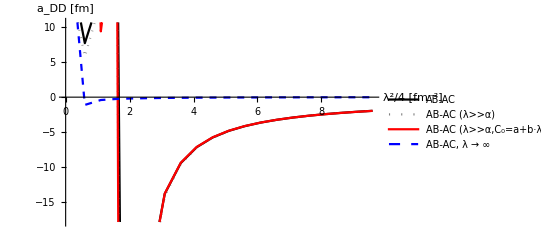

```mathematica
ListLinePlot[{Transpose[{Λl,add0}],Transpose[{Λl,add1}],Transpose[{Λl,add2}],Transpose[{Λl,add3}]},AxesLabel->{"λ^2/4 [fm^-2]","a_DD [fm]"},PlotStyle->{{Black,Thin},{Gray,Dotted,Thick},{Red,Opacity->0.2},{Blue,Dashed}},PlotLegends->{"AB-AC","AB-AC (λ>>α)","AB-AC (λ>>α,C_0=a+b·λ D_0=a+b·λ+c·λ^2+d·λ^3)","AB-AC, λ → ∞"}]
```

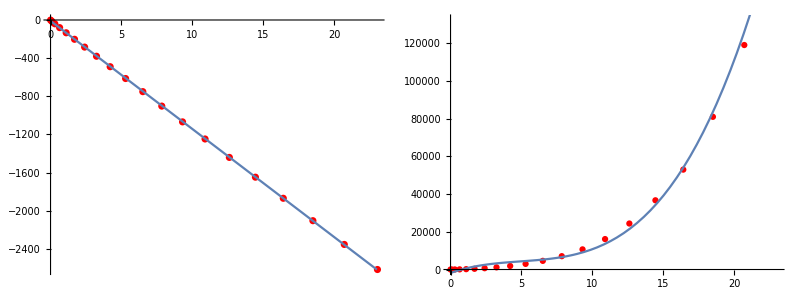

```mathematica
linm=Fit[dataC,{1,x},x];nlinm=Fit[dataD,{1,x,x^2,x^3},x];
Grid[{{Show[ListPlot[dataC, PlotStyle->Red], Plot[{linm},{x,0,23}]],Show[ListPlot[dataD, PlotStyle->Red], Plot[{nlinm},{x,0,23}]]}}]
```